2

2

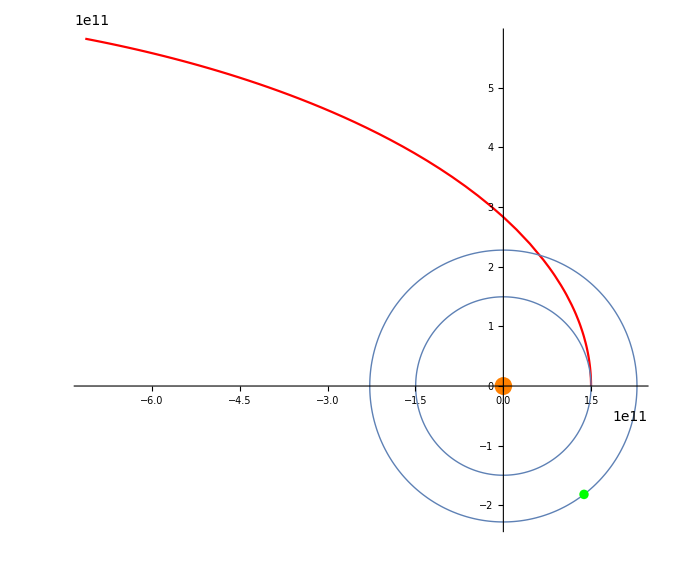

```mathematica
(* 以下为常量 *)
MS := 1.9891 * 10 ^ 30;
m := 2000;
G := 6.67259 * 10 ^ (-11);
mu := MS * G;
RE := 1.496 * 10 ^ 11;
RM := 2.2794 * 10 ^ 11;
ME := 5.965 * 10 ^ 24;
MM := 6.4219 * 10 ^ 23; 
TM := 5.93568 * 10 ^ 7;

(* 以下为初始条件 *)
X0X := RE; (* 初始x位置 *)
Y0Y := 0;(* 初始y位置 *)
V0X := 0; (* 初始x速度 *)
V0Y := 11200+29790; (* 初始y速度 *)

(* 以下为末状态的时刻 *)
tend :=50640000;

(* 以下为部分表达式 *)
cosTheta[t_] := x[t]/(√(x[t]^2+y[t]^2));
sinTheta[t_]:= y[t]/(√(x[t]^2+y[t]^2));
rS[t_] := Sqrt[ x[t]^2 + y[t]^2 ]; 

(* 以下是微分方程 *)
eqX := (   (mu*x[t])/rS[t]^3  + x''[t] == 0  );
eqY := (   (mu*y[t])/rS[t]^3  + y''[t] == 0  );
Print[2];
sol = NDSolve[  {eqX,eqY,x[0]== X0X,x'[0]== V0X, y[0] == Y0Y, y'[0]== V0Y } , {x[t],y[t]} , {t,0,tend} ];
Print[2];
g1 = ParametricPlot[ Evaluate[ {x[t],y[t]}/.sol ] , {t,0,tend} , PlotRange->All , PlotStyle->{Red}];
g2 = ParametricPlot[ Evaluate[ {RE*Cos[t1], RE*Sin[t1]} ] , {t1 , 0 , 2*Pi} , PlotRange->All , PlotStyle->Thick , PlotLabel->Earth ];
g3 = ParametricPlot[ Evaluate[ {RM*Cos[t2], RM*Sin[t2]} ] , {t2 , 0 , 2*Pi} , PlotRange->All , PlotStyle->Thick , PlotLabel->Mars ];
g4 = Graphics[ {Orange,Disk[{0,0},15*10^9]} ];
g5 = Graphics[ {Green , Disk[ {RM*Cos[tend/(TM)*2*Pi],RM*Sin[tend/(TM)*2*Pi]} , 80*10^8 ] } ];
(*
Manipulate[
Show[
g1,g2,g3,g4,
Graphics[  Disk[ {RE*Cos[t3],RE*Sin[t3]}, 50*10^8 ]  ]
],
{t3 , 0, 100}
]
*)
Show[g1,g2,g3,g4,g5]
```

```mathematica
sol
```

{{x[t]→                                    7
InterpolatingFunction[{{0., 5.064 10 }}, <>][t],y[t]→                                    7
InterpolatingFunction[{{0., 5.064 10 }}, <>][t]}}

```mathematica
x1[t_]=x[t]/.sol
```

{                                    7
InterpolatingFunction[{{0., 5.064 10 }}, <>][t]}

```mathematica
x1[1000]
```

{1.496×10^11}

```mathematica
y1[t_]=y[t]/.sol
```

{                                    7
InterpolatingFunction[{{0., 5.064 10 }}, <>][t]}

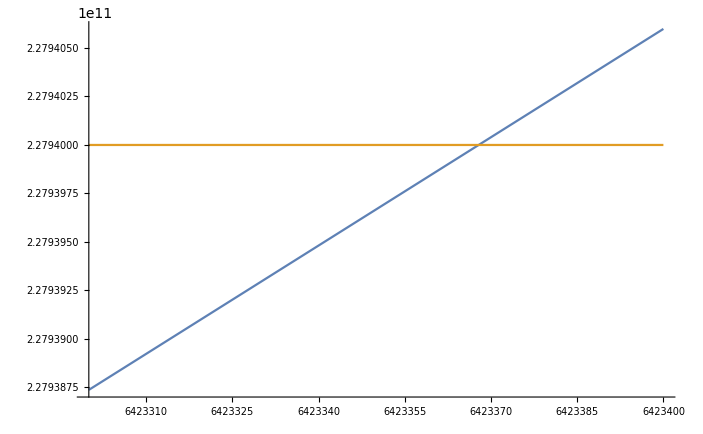

```mathematica
Plot[{Sqrt[x1[t]^2+y1[t]^2],RM},{t,6423300,6423400}]
```

```mathematica
solC=FindRoot[{x1[t]^2+y1[t]^2==RM^2},{t,6423400}]
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{t→6.42337×10^6}

```mathematica
t0=t/.solC
```

6.42337×10^6

```mathematica
t0
```

6.42337×10^6

```mathematica
2Pi/TM*t0
```

0.679942

```mathematica
ArcCos[x1[t0]/RM]
```

{1.29554}

```mathematica
Sqrt[2*G*MM/3395000]
```

5024.28

```mathematica
24
32
```